```mathematica
(*Computing classicality for the paper window function*)
u=(√(-π τ))/2 HankelH1[3/2,-k τ]//FunctionExpand
ϕ=u/(-1/H/τ)
uc=(√(-π τ))/2 HankelH2[3/2,-k τ]//FunctionExpand
ϕc=uc/(-1/H/τ)
```

-(ⅇ^(-ⅈ k τ) √-τ (-ⅈ+k τ))/(√2 k τ √(-k τ))

(ⅇ^(-ⅈ k τ) H √-τ (-ⅈ+k τ))/(√2 k √(-k τ))

-(ⅇ^(ⅈ k τ) √-τ (ⅈ+k τ))/(√2 k τ √(-k τ))

(ⅇ^(ⅈ k τ) H √-τ (ⅈ+k τ))/(√2 k √(-k τ))

```mathematica
(*Computing classicality for the case ϕϕ*)                                                  (*Already done by Dr Noorbala*)
```

```mathematica
(ϕ/.{τ->τ1})(ϕc/.{τ->τ2})//FunctionExpand//FullSimplify
```

(ⅇ^(-ⅈ k (τ1-τ2)) H^2 √-τ1 (-ⅈ+k τ1) √-τ2 (ⅈ+k τ2))/(2 k^2 √(-k τ1) √(-k τ2))

```mathematica
Integrate[(ⅇ^(-ⅈ k τ1+ⅈ k τ2) H^2 (-ⅈ+k τ1)  (ⅈ+k τ2))/(2 k^3) (4π)/(2π)^3 k^2 (-k τ1)/σ 1/(2 δ)(-k τ2)/σ 1/(2 δ),{k,k1,k2}]
```

1/(16 π^2 δ^2 σ^2 (τ1-τ2)^4)H^2 τ1 τ2 (ⅇ^(-ⅈ k1 (τ1-τ2)) (-ⅈ k1^3 τ1 (τ1-τ2)^3 τ2+k1^2 (τ1-τ2)^2 (τ1^2-5 τ1 τ2+τ2^2)-3 (τ1^2-4 τ1 τ2+τ2^2)-3 ⅈ k1 (τ1-τ2) (τ1^2-4 τ1 τ2+τ2^2))+ⅇ^(-ⅈ k2 (τ1-τ2)) (ⅈ k2^3 τ1 (τ1-τ2)^3 τ2-k2^2 (τ1-τ2)^2 (τ1^2-5 τ1 τ2+τ2^2)+3 (τ1^2-4 τ1 τ2+τ2^2)+3 ⅈ k2 (τ1-τ2) (τ1^2-4 τ1 τ2+τ2^2)))

```mathematica
(H^2 τ1 τ2 (ⅇ^(-ⅈ k1 (τ1-τ2)) (-ⅈ k1^3 τ1 (τ1-τ2)^3 τ2+k1^2 (τ1-τ2)^2 (τ1^2-5 τ1 τ2+τ2^2)-3 (τ1^2-4 τ1 τ2+τ2^2)-3 ⅈ k1 (τ1-τ2) (τ1^2-4 τ1 τ2+τ2^2))+ⅇ^(-ⅈ k2 (τ1-τ2)) (ⅈ k2^3 τ1 (τ1-τ2)^3 τ2-k2^2 (τ1-τ2)^2 (τ1^2-5 τ1 τ2+τ2^2)+3 (τ1^2-4 τ1 τ2+τ2^2)+3 ⅈ k2 (τ1-τ2) (τ1^2-4 τ1 τ2+τ2^2))))/(16 π^2 δ^2 σ^2 (τ1-τ2)^4)/.{k1->-σ/τ2(1-δ),k2->-σ/τ1(1+δ)}//Simplify
```

1/(16 π^2 δ^2 σ^2 (τ1-τ2)^4)H^2 τ1 τ2 (-1/τ1^2 ⅇ^((ⅈ (1+δ) σ (τ1-τ2))/τ1) (ⅈ (1+δ)^3 σ^3 (τ1-τ2)^3 τ2+(1+δ)^2 σ^2 (τ1-τ2)^2 (τ1^2-5 τ1 τ2+τ2^2)-3 τ1^2 (τ1^2-4 τ1 τ2+τ2^2)+3 ⅈ (1+δ) σ τ1 (τ1-τ2) (τ1^2-4 τ1 τ2+τ2^2))+1/τ2^2 ⅇ^(-(ⅈ (-1+δ) σ (τ1-τ2))/τ2) (-ⅈ (-1+δ)^3 σ^3 τ1 (τ1-τ2)^3+(-1+δ)^2 σ^2 (τ1-τ2)^2 (τ1^2-5 τ1 τ2+τ2^2)-3 ⅈ (-1+δ) σ (τ1-τ2) τ2 (τ1^2-4 τ1 τ2+τ2^2)-3 τ2^2 (τ1^2-4 τ1 τ2+τ2^2)))

```mathematica
Series[(H^2 τ1 τ2 (-1/τ1^2 ⅇ^((ⅈ (1+δ) σ (τ1-τ2))/τ1) (ⅈ (1+δ)^3 σ^3 (τ1-τ2)^3 τ2+(1+δ)^2 σ^2 (τ1-τ2)^2 (τ1^2-5 τ1 τ2+τ2^2)-3 τ1^2 (τ1^2-4 τ1 τ2+τ2^2)+3 ⅈ (1+δ) σ τ1 (τ1-τ2) (τ1^2-4 τ1 τ2+τ2^2))+1/τ2^2 ⅇ^(-(ⅈ (-1+δ) σ (τ1-τ2))/τ2) (-ⅈ (-1+δ)^3 σ^3 τ1 (τ1-τ2)^3+(-1+δ)^2 σ^2 (τ1-τ2)^2 (τ1^2-5 τ1 τ2+τ2^2)-3 ⅈ (-1+δ) σ (τ1-τ2) τ2 (τ1^2-4 τ1 τ2+τ2^2)-3 τ2^2 (τ1^2-4 τ1 τ2+τ2^2))))/(16 π^2 δ^2 σ^2 (τ1-τ2)^4),{σ,0,1}]
```

-(H^2 (τ1^2-2 δ τ1^2+δ^2 τ1^2-τ2^2-2 δ τ2^2-δ^2 τ2^2))/(32 (π^2 δ^2 τ1 τ2))+O[σ]^2

```mathematica
X=(H^2 τ1 τ2 (-1/τ1^2 ⅇ^((ⅈ (1+δ) σ (τ1-τ2))/τ1) (ⅈ (1+δ)^3 σ^3 (τ1-τ2)^3 τ2+(1+δ)^2 σ^2 (τ1-τ2)^2 (τ1^2-5 τ1 τ2+τ2^2)-3 τ1^2 (τ1^2-4 τ1 τ2+τ2^2)+3 ⅈ (1+δ) σ τ1 (τ1-τ2) (τ1^2-4 τ1 τ2+τ2^2))+1/τ2^2 ⅇ^(-(ⅈ (-1+δ) σ (τ1-τ2))/τ2) (-ⅈ (-1+δ)^3 σ^3 τ1 (τ1-τ2)^3+(-1+δ)^2 σ^2 (τ1-τ2)^2 (τ1^2-5 τ1 τ2+τ2^2)-3 ⅈ (-1+δ) σ (τ1-τ2) τ2 (τ1^2-4 τ1 τ2+τ2^2)-3 τ2^2 (τ1^2-4 τ1 τ2+τ2^2))))/(16 π^2 δ^2 σ^2 (τ1-τ2)^4);

Series[X,{σ,0,3}]
```

```mathematica
-(H^2 (τ1^2-2 δ τ1^2+δ^2 τ1^2-τ2^2-2 δ τ2^2-δ^2 τ2^2))/(32 (π^2 δ^2 τ1 τ2))+(H^2 τ1 τ2 (((1+δ)^4 (τ1-τ2)^4 (τ1^2+τ2^2))/(8 τ1^4)-((-1+δ)^4 (-τ1+τ2)^4 (τ1^2+τ2^2))/(8 τ2^4)) σ^2)/(16 π^2 δ^2 (τ1-τ2)^4)+(H^2 τ1 τ2 ((ⅈ (1+δ)^5 (τ1-τ2)^5 (τ1^2+τ1 τ2+τ2^2))/(15 τ1^5)-(ⅈ (-1+δ)^5 (-τ1+τ2)^5 (τ1^2+τ1 τ2+τ2^2))/(15 τ2^5)) σ^3)/(16 π^2 δ^2 (τ1-τ2)^4)+O[σ]^4
```

-(H^2 (τ1^2-2 δ τ1^2+δ^2 τ1^2-τ2^2-2 δ τ2^2-δ^2 τ2^2))/(32 (π^2 δ^2 τ1 τ2))+(H^2 τ1 τ2 (((1+δ)^4 (τ1-τ2)^4 (τ1^2+τ2^2))/(8 τ1^4)-((-1+δ)^4 (-τ1+τ2)^4 (τ1^2+τ2^2))/(8 τ2^4)) σ^2)/(16 π^2 δ^2 (τ1-τ2)^4)+(H^2 τ1 τ2 ((ⅈ (1+δ)^5 (τ1-τ2)^5 (τ1^2+τ1 τ2+τ2^2))/(15 τ1^5)-(ⅈ (-1+δ)^5 (-τ1+τ2)^5 (τ1^2+τ1 τ2+τ2^2))/(15 τ2^5)) σ^3)/(16 π^2 δ^2 (τ1-τ2)^4)+O[σ]^4

```mathematica
C1= ((H^2 τ1 τ2 ((ⅈ (1+δ)^5 (τ1-τ2)^5 (τ1^2+τ1 τ2+τ2^2))/(15 τ1^5)-(ⅈ (-1+δ)^5 (-τ1+τ2)^5 (τ1^2+τ1 τ2+τ2^2))/(15 τ2^5)) σ^3)/(16 π^2 δ^2 (τ1-τ2)^4))/(-(H^2 (τ1^2-2 δ τ1^2+δ^2 τ1^2-τ2^2-2 δ τ2^2-δ^2 τ2^2))/(32 (π^2 δ^2 τ1 τ2)))//FullSimplify      (*C1 is inverse of what we already defined as Classicality*)   (*the term multiplied by σ^2 is ommitted by hand since σ<1*)
```

```mathematica
-(2 ⅈ σ^3 (τ1^3-τ2^3) ((-1+δ)^4 τ1^4-(-1+δ)^3 (1+δ) τ1^3 τ2+(-1+δ^2)^2 τ1^2 τ2^2-(-1+δ) (1+δ)^3 τ1 τ2^3+(1+δ)^4 τ2^4))/(15 τ1^3 τ2^3 ((-1+δ) τ1-(1+δ) τ2))
```

```mathematica
(*we substitute (1-δ) τ1 = T1 & (1+δ) τ2= T2, then we have C1 as follows *)

(2 σ^3 (τ1^3-τ2^3))/(15 τ1^3 τ2^3) ((T1^4+T1^3 T2+T1^2 T2^2+T1 T2^3+T2^4)/(T1 +T2))
```

```mathematica
C1= ((H^2 τ1 τ2 ((ⅈ (1+δ)^5 (τ1-τ2)^5 (τ1^2+τ1 τ2+τ2^2))/(15 τ1^5)-(ⅈ (-1+δ)^5 (-τ1+τ2)^5 (τ1^2+τ1 τ2+τ2^2))/(15 τ2^5)) σ^3)/(16 π^2 δ^2 (τ1-τ2)^4))/(-(H^2 (τ1^2-2 δ τ1^2+δ^2 τ1^2-τ2^2-2 δ τ2^2-δ^2 τ2^2))/(32 (π^2 δ^2 τ1 τ2)))//FullSimplify
```

-(2 ⅈ σ^3 (τ1^3-τ2^3) ((-1+δ)^4 τ1^4-(-1+δ)^3 (1+δ) τ1^3 τ2+(-1+δ^2)^2 τ1^2 τ2^2-(-1+δ) (1+δ)^3 τ1 τ2^3+(1+δ)^4 τ2^4))/(15 τ1^3 τ2^3 ((-1+δ) τ1-(1+δ) τ2))

```mathematica
C11 = (-(H^2 (τ1^2-2 δ τ1^2+δ^2 τ1^2-τ2^2-2 δ τ2^2-δ^2 τ2^2))/(32 (π^2 δ^2 τ1 τ2)))/((H^2 τ1 τ2 ((ⅈ (1+δ)^5 (τ1-τ2)^5 (τ1^2+τ1 τ2+τ2^2))/(15 τ1^5)-(ⅈ (-1+δ)^5 (-τ1+τ2)^5 (τ1^2+τ1 τ2+τ2^2))/(15 τ2^5)) σ^3)/(16 π^2 δ^2 (τ1-τ2)^4)) //FullSimplify
```

(15 ⅈ τ1^3 τ2^3 ((-1+δ) τ1-(1+δ) τ2))/(2 σ^3 (τ1-τ2) (τ1^2+τ1 τ2+τ2^2) ((-1+δ)^4 τ1^4-(-1+δ)^3 (1+δ) τ1^3 τ2+(-1+δ^2)^2 τ1^2 τ2^2-(-1+δ) (1+δ)^3 τ1 τ2^3+(1+δ)^4 τ2^4))

```mathematica
C11 = (-((H^2 (τ1^2-2 δ τ1^2+δ^2 τ1^2-τ2^2-2 δ τ2^2-δ^2 τ2^2))/(32 (π^2 δ^2 τ1 τ2))))/1/(16 π^2 δ^2 (τ1-τ2)^4)H^2 τ1 τ2 ((ⅈ (1+δ)^5 (τ1-τ2)^5 (τ1^2+τ1 τ2+τ2^2))/(15 τ1^5)-(ⅈ (-1+δ)^5 (-τ1+τ2)^5 (τ1^2+τ1 τ2+τ2^2))/(15 τ2^5)) σ^3//FullSimplify
```

```mathematica
(*Newww*****************************************************************************************************)
```

```mathematica
(15  τ1^3 τ2^3 ((-1+δ) τ1-(1+δ) τ2))/(2 σ^3 (τ1-τ2) (τ1^2+τ1 τ2+τ2^2) ((-1+δ)^4 τ1^4-(-1+δ)^3 (1+δ) τ1^3 τ2+(-1+δ^2)^2 τ1^2 τ2^2-(-1+δ) (1+δ)^3 τ1 τ2^3+(1+δ)^4 τ2^4)) /.δ->0//FullSimplify
```

-(15 τ1^3 τ2^3 (τ1+τ2))/(2 σ^3 (τ1^7+τ1^6 τ2+τ1^5 τ2^2-τ1^2 τ2^5-τ1 τ2^6-τ2^7))

```mathematica
(*Define the classicality function*)classicality3D[τ1_,τ2_,δ_,σ_]:=(15 τ1^3 τ2^3 ((-1+δ) τ1-(1+δ) τ2))/(2 σ^3 (τ1-τ2) (τ1^2+τ1 τ2+τ2^2) ((-1+δ)^4 τ1^4-(-1+δ)^3 (1+δ) τ1^3 τ2+(-1+δ^2)^2 τ1^2 τ2^2-(-1+δ) (1+δ)^3 τ1 τ2^3+(1+δ)^4 τ2^4))

(*Create the 3D plot*)
Plot3D[classicality3D[τ1,τ2,0.5,1.0],(*δ=0.5,σ=1.0*){τ1,0.1,5},{τ2,0.1,5},(*Avoid τ1=τ2 (singularity)*)PlotRange->All,(*Or use specific range like {-10,10}*)(*Styling options*)PlotPoints->50,(*Higher=smoother but slower*)MaxRecursion->3,AxesLabel->{Style["τ1",14,Bold],Style["τ2",14,Bold],Style["Classicality",14,Bold]},PlotLabel->Style["Classicality Factor C(τ1, τ2)",16,Bold],ColorFunction->"TemperatureMap",(*Or "Rainbow","SunsetColors"*)Mesh->True,MeshFunctions->{#3&},(*Mesh lines on constant C*)(*Better view angles*)ViewPoint->{3,2,1},(*Adjust viewpoint*)BoxRatios->{1,1,1},(*Handle singularities near τ1=τ2*)Exclusions->{τ1==τ2},(*Avoid division by zero*)ExclusionsStyle->Directive[Red,Thick]]
```

-Graphics3D-

```mathematica
Manipulate[Plot3D[classicality3D[τ1,τ2,δ,σ],{τ1,τ1min,τ1max},{τ2,τ2min,τ2max},PlotRange->plotRange,AxesLabel->{"τ1","τ2","C(τ1,τ2)"},PlotLabel->StringForm["δ = `1`, σ = `2`",δ,σ],ColorFunction->"Rainbow",Mesh->True,PerformanceGoal->"Quality",Exclusions->{τ1==τ2}],(*Control sliders*){{δ,0.5,"δ"},-2,2,0.1,Appearance->"Labeled"},{{σ,1.0,"σ"},0.1,5,0.1,Appearance->"Labeled"},{{τ1min,0.1,"τ1 min"},0.01,1,0.01,Appearance->"Labeled"},{{τ1max,3,"τ1 max"},1,10,0.1,Appearance->"Labeled"},{{τ2min,0.1,"τ2 min"},0.01,1,0.01,Appearance->"Labeled"},{{τ2max,3,"τ2 max"},1,10,0.1,Appearance->"Labeled"},{{plotRange,{-5,5},"Plot Range"},{-20,-10,-5,-2,-1,1,2,5,10,20}}]
```

Power::infy: Infinite expression 1/0. encountered.

Power::infy: Infinite expression 1/0. encountered.

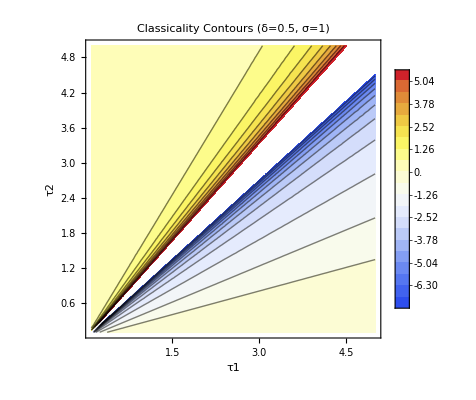

```mathematica
ContourPlot[classicality3D[τ1,τ2,0.5,1.0],{τ1,0.1,5},{τ2,0.1,5},PlotLegends->Automatic,FrameLabel->{"τ1","τ2"},PlotLabel->"Classicality Contours (δ=0.5, σ=1)",ColorFunction->"TemperatureMap",Contours->20,Exclusions->{τ1==τ2}]
```

```mathematica
(*Classicality for the case  ϕv        ******************************************************************************************)
```

```mathematica
(ϕ/.{τ->τ1})(ϕcd/.{τ->τ2}) ;
ϕ= (ⅇ^(-ⅈ k τ) H (-ⅈ+k τ))/(√2 k √k)//FullSimplify
ϕcd =D[(ⅇ^(ⅈ k τ) H (ⅈ+k τ))/(√2 k √k), τ]//FullSimplify
```

(ⅇ^(-ⅈ k τ) H (-ⅈ+k τ))/(√2 k^(3/2))

(ⅈ ⅇ^(ⅈ k τ) H √k τ)/(√2)

```mathematica
(ϕ/.{τ->τ1})(ϕcd/.{τ->τ2})//FunctionExpand
```

(ⅈ ⅇ^(-ⅈ k τ1+ⅈ k τ2) H^2 (-ⅈ+k τ1) τ2)/(2 k)

```mathematica
Integrate[(ⅈ ⅇ^(-ⅈ k τ1+ⅈ k τ2) H^2 (-ⅈ+k τ1) τ2)/(2 k)(4π)/(2π)^3 k^2 (-k τ1)/σ 1/(2 δ)(-k τ2)/σ 1/(2 δ),{k,k1,k2}]
```

1/(16 π^2 δ^2 σ^2 (τ1-τ2)^5)H^2 τ1 (ⅈ τ1 (-ⅇ^(-ⅈ k1 (τ1-τ2)) (24 ⅈ+k1 (-24+k1 (-12 ⅈ+k1 (4+ⅈ k1 (τ1-τ2)) (τ1-τ2)) (τ1-τ2)) (τ1-τ2))+ⅇ^(-ⅈ k2 (τ1-τ2)) (24 ⅈ+k2 (-24+k2 (-12 ⅈ+k2 (4+ⅈ k2 (τ1-τ2)) (τ1-τ2)) (τ1-τ2)) (τ1-τ2)))+(ⅇ^(-ⅈ k1 (τ1-τ2)) (6-k1 (-6 ⅈ+k1 (3+ⅈ k1 (τ1-τ2)) (τ1-τ2)) (τ1-τ2))+ⅇ^(-ⅈ k2 (τ1-τ2)) (-6+k2 (-6 ⅈ+k2 (3+ⅈ k2 (τ1-τ2)) (τ1-τ2)) (τ1-τ2))) (τ1-τ2)) τ2^2

```mathematica
ϕvintegral=1/(16 π^2 δ^2 σ^2 (τ1-τ2)^5)H^2 τ1 (ⅈ τ1 (-ⅇ^(-ⅈ k1 (τ1-τ2)) (24 ⅈ+k1 (-24+k1 (-12 ⅈ+k1 (4+ⅈ k1 (τ1-τ2)) (τ1-τ2)) (τ1-τ2)) (τ1-τ2))+ⅇ^(-ⅈ k2 (τ1-τ2)) (24 ⅈ+k2 (-24+k2 (-12 ⅈ+k2 (4+ⅈ k2 (τ1-τ2)) (τ1-τ2)) (τ1-τ2)) (τ1-τ2)))+(ⅇ^(-ⅈ k1 (τ1-τ2)) (6-k1 (-6 ⅈ+k1 (3+ⅈ k1 (τ1-τ2)) (τ1-τ2)) (τ1-τ2))+ⅇ^(-ⅈ k2 (τ1-τ2)) (-6+k2 (-6 ⅈ+k2 (3+ⅈ k2 (τ1-τ2)) (τ1-τ2)) (τ1-τ2))) (τ1-τ2)) τ2^2/.{k1->-σ/τ2(1-δ),k2->-σ/τ1(1+δ)}//Simplify
```

1/(16 π^2 δ^2 σ^2 τ1^2 (τ1-τ2)^5 τ2^2)H^2 (-((τ1-τ2) τ2 (ⅇ^((ⅈ (1+δ) σ (τ1-τ2))/τ1) (6 τ1^3-(1+δ) σ (6 ⅈ τ1^2+(1+δ) σ (3 τ1-ⅈ (1+δ) σ (τ1-τ2)) (τ1-τ2)) (τ1-τ2)) τ2^3-ⅇ^(-(ⅈ (-1+δ) σ (τ1-τ2))/τ2) τ1^3 (6 τ2^3+(1-δ) σ (τ1-τ2) ((1-δ) σ (-ⅈ (-1+δ) σ (τ1-τ2)-3 τ2) (τ1-τ2)-6 ⅈ τ2^2))))+ⅈ (ⅇ^((ⅈ (1+δ) σ (τ1-τ2))/τ1) (24 ⅈ τ1^4+(1+δ) σ (24 τ1^3-(1+δ) σ (12 ⅈ τ1^2+(1+δ) σ (4 τ1-ⅈ (1+δ) σ (τ1-τ2)) (τ1-τ2)) (τ1-τ2)) (τ1-τ2)) τ2^4-ⅇ^(-(ⅈ (-1+δ) σ (τ1-τ2))/τ2) τ1^4 (24 ⅈ τ2^4+(1-δ) σ (τ1-τ2) (24 τ2^3+(1-δ) σ (τ1-τ2) ((1-δ) σ (-ⅈ (-1+δ) σ (τ1-τ2)-4 τ2) (τ1-τ2)-12 ⅈ τ2^2)))))

```mathematica
X= Series[ϕvintegral, {σ,0,3}]
```

```mathematica
(H^2 (-((-1+δ)^4 τ1^3 (τ1-τ2)^4)/(4 τ2)+((1+δ)^4 (τ1-τ2)^4 τ2^3)/(4 τ1)) σ^2)/(16 π^2 δ^2 τ1^2 (τ1-τ2)^4 τ2)-1/(80 π^2 δ^2 τ1^4 τ2^2)ⅈ H^2 (-τ1^5+5 δ τ1^5-10 δ^2 τ1^5+10 δ^3 τ1^5-5 δ^4 τ1^5+δ^5 τ1^5+τ2^5+5 δ τ2^5+10 δ^2 τ2^5+10 δ^3 τ2^5+5 δ^4 τ2^5+δ^5 τ2^5) σ^3+O[σ]^4//FullSimplify
```

-((H^2 ((-1+δ)^4 τ1^4-(1+δ)^4 τ2^4)) σ^2)/(64 (π^2 δ^2 τ1^3 τ2^2))-(ⅈ H^2 ((-1+δ)^5 τ1^5+(1+δ)^5 τ2^5) σ^3)/(80 π^2 δ^2 τ1^4 τ2^2)+O[σ]^4

```mathematica
(*avval simplify kardam baad kasre classico neveshtam*)
(((H^2 ((-1+δ)^4 τ1^4-(1+δ)^4 τ2^4)) σ^2)/(64 (π^2 δ^2 τ1^3 τ2^2)))/((H^2 ((-1+δ)^5 τ1^5+(1+δ)^5 τ2^5) σ^3)/(80 π^2 δ^2 τ1^4 τ2^2))
```

(5 τ1 ((-1+δ)^4 τ1^4-(1+δ)^4 τ2^4))/(4 σ ((-1+δ)^5 τ1^5+(1+δ)^5 τ2^5))

```mathematica
(* hala avval taghsim mikonam baad full simplify mikonam*)
(((H^2 (-((-1+δ)^4 τ1^3 (τ1-τ2)^4)/(4 τ2)+((1+δ)^4 (τ1-τ2)^4 τ2^3)/(4 τ1)) σ^2)/(16 π^2 δ^2 τ1^2 (τ1-τ2)^4 τ2)-1/(80 π^2 δ^2 τ1^4 τ2^2))/(H^2 (-τ1^5+5 δ τ1^5-10 δ^2 τ1^5+10 δ^3 τ1^5-5 δ^4 τ1^5+δ^5 τ1^5+τ2^5+5 δ τ2^5+10 δ^2 τ2^5+10 δ^3 τ2^5+5 δ^4 τ2^5+δ^5 τ2^5) σ^3+O[σ]^4))
```

```mathematica
-(1/(80 (H^2 π^2 δ^2 τ1^4 τ2^2 (-τ1^5+5 δ τ1^5-10 δ^2 τ1^5+10 δ^3 τ1^5-5 δ^4 τ1^5+δ^5 τ1^5+τ2^5+5 δ τ2^5+10 δ^2 τ2^5+10 δ^3 τ2^5+5 δ^4 τ2^5+δ^5 τ2^5)) σ^3))+1/O[σ]^2//FullSimplify
```

-1/(80 (H^2 π^2 δ^2 τ1^4 τ2^2 ((-1+δ)^5 τ1^5+(1+δ)^5 τ2^5)) σ^3)+1/O[σ]^2

```mathematica
(*Classicality for ϕv integral*)
RealPart = (3 (H^2 (-τ1)^(3/2) (5 τ1-τ2) (-τ2)^(3/2) (√(-((-1+δ) σ)) √((1+δ) σ)-√(-((-1+δ) σ τ1)/τ2) √(((1+δ) σ τ2)/τ1))))/(8 (π^2 δ^2 √((1+δ) σ) (τ1-τ2)^5 √(-((-1+δ) σ τ1)/τ2)) σ^2)+(H^2 (√(-((-1+δ) σ)) √((1+δ) σ) τ1^4-4 δ √(-((-1+δ) σ)) √((1+δ) σ) τ1^4+6 δ^2 √(-((-1+δ) σ)) √((1+δ) σ) τ1^4-4 δ^3 √(-((-1+δ) σ)) √((1+δ) σ) τ1^4+δ^4 √(-((-1+δ) σ)) √((1+δ) σ) τ1^4-√(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1)-4 δ √(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1)-6 δ^2 √(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1)-4 δ^3 √(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1)-δ^4 √(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1)) σ^2)/(64 π^2 δ^2 √((1+δ) σ) (-τ1)^(5/2) √(-((-1+δ) σ τ1)/τ2) (-τ2)^(5/2))
ImaginaryPart= ( H^2 (-√(-((-1+δ) σ)) √((1+δ) σ) τ1^5+5 δ √(-((-1+δ) σ)) √((1+δ) σ) τ1^5-10 δ^2 √(-((-1+δ) σ)) √((1+δ) σ) τ1^5+10 δ^3 √(-((-1+δ) σ)) √((1+δ) σ) τ1^5-5 δ^4 √(-((-1+δ) σ)) √((1+δ) σ) τ1^5+δ^5 √(-((-1+δ) σ)) √((1+δ) σ) τ1^5+√(-((-1+δ) σ τ1)/τ2) τ2^5 √(((1+δ) σ τ2)/τ1)+5 δ √(-((-1+δ) σ τ1)/τ2) τ2^5 √(((1+δ) σ τ2)/τ1)+10 δ^2 √(-((-1+δ) σ τ1)/τ2) τ2^5 √(((1+δ) σ τ2)/τ1)+10 δ^3 √(-((-1+δ) σ τ1)/τ2) τ2^5 √(((1+δ) σ τ2)/τ1)+5 δ^4 √(-((-1+δ) σ τ1)/τ2) τ2^5 √(((1+δ) σ τ2)/τ1)+δ^5 √(-((-1+δ) σ τ1)/τ2) τ2^5 √(((1+δ) σ τ2)/τ1)) σ^3)/(80 π^2 δ^2 √((1+δ) σ) (-τ1)^(7/2) √(-((-1+δ) σ τ1)/τ2) (-τ2)^(5/2))
```

(3 H^2 (-τ1)^(3/2) (5 τ1-τ2) (-τ2)^(3/2) (√(-((-1+δ) σ)) √((1+δ) σ)-√(-((-1+δ) σ τ1)/τ2) √(((1+δ) σ τ2)/τ1)))/(8 π^2 δ^2 σ^2 √((1+δ) σ) (τ1-τ2)^5 √(-((-1+δ) σ τ1)/τ2))+(H^2 σ^2 (√(-((-1+δ) σ)) √((1+δ) σ) τ1^4-4 δ √(-((-1+δ) σ)) √((1+δ) σ) τ1^4+6 δ^2 √(-((-1+δ) σ)) √((1+δ) σ) τ1^4-4 δ^3 √(-((-1+δ) σ)) √((1+δ) σ) τ1^4+δ^4 √(-((-1+δ) σ)) √((1+δ) σ) τ1^4-√(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1)-4 δ √(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1)-6 δ^2 √(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1)-4 δ^3 √(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1)-δ^4 √(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1)))/(64 π^2 δ^2 √((1+δ) σ) (-τ1)^(5/2) √(-((-1+δ) σ τ1)/τ2) (-τ2)^(5/2))

(H^2 σ^3 (-√(-((-1+δ) σ)) √((1+δ) σ) τ1^5+5 δ √(-((-1+δ) σ)) √((1+δ) σ) τ1^5-10 δ^2 √(-((-1+δ) σ)) √((1+δ) σ) τ1^5+10 δ^3 √(-((-1+δ) σ)) √((1+δ) σ) τ1^5-5 δ^4 √(-((-1+δ) σ)) √((1+δ) σ) τ1^5+δ^5 √(-((-1+δ) σ)) √((1+δ) σ) τ1^5+√(-((-1+δ) σ τ1)/τ2) τ2^5 √(((1+δ) σ τ2)/τ1)+5 δ √(-((-1+δ) σ τ1)/τ2) τ2^5 √(((1+δ) σ τ2)/τ1)+10 δ^2 √(-((-1+δ) σ τ1)/τ2) τ2^5 √(((1+δ) σ τ2)/τ1)+10 δ^3 √(-((-1+δ) σ τ1)/τ2) τ2^5 √(((1+δ) σ τ2)/τ1)+5 δ^4 √(-((-1+δ) σ τ1)/τ2) τ2^5 √(((1+δ) σ τ2)/τ1)+δ^5 √(-((-1+δ) σ τ1)/τ2) τ2^5 √(((1+δ) σ τ2)/τ1)))/(80 π^2 δ^2 √((1+δ) σ) (-τ1)^(7/2) √(-((-1+δ) σ τ1)/τ2) (-τ2)^(5/2))

```mathematica
Z= RealPart/ImaginaryPart
```

```mathematica
(80 π^2 δ^2 √((1+δ) σ) (-τ1)^(7/2) √(-((-1+δ) σ τ1)/τ2) (-τ2)^(5/2) ((3 H^2 (-τ1)^(3/2) (5 τ1-τ2) (-τ2)^(3/2) (√(-((-1+δ) σ)) √((1+δ) σ)-√(-((-1+δ) σ τ1)/τ2) √(((1+δ) σ τ2)/τ1)))/(8 π^2 δ^2 σ^2 √((1+δ) σ) (τ1-τ2)^5 √(-((-1+δ) σ τ1)/τ2))+1/(64 π^2 δ^2 √((1+δ) σ) (-τ1)^(5/2) √(-((-1+δ) σ τ1)/τ2) (-τ2)^(5/2))H^2 σ^2 (√(-((-1+δ) σ)) √((1+δ) σ) τ1^4-4 δ √(-((-1+δ) σ)) √((1+δ) σ) τ1^4+6 δ^2 √(-((-1+δ) σ)) √((1+δ) σ) τ1^4-4 δ^3 √(-((-1+δ) σ)) √((1+δ) σ) τ1^4+δ^4 √(-((-1+δ) σ)) √((1+δ) σ) τ1^4-√(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1)-4 δ √(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1)-6 δ^2 √(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1)-4 δ^3 √(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1)-δ^4 √(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1))))/(H^2 σ^3 (-√(-((-1+δ) σ)) √((1+δ) σ) τ1^5+5 δ √(-((-1+δ) σ)) √((1+δ) σ) τ1^5-10 δ^2 √(-((-1+δ) σ)) √((1+δ) σ) τ1^5+10 δ^3 √(-((-1+δ) σ)) √((1+δ) σ) τ1^5-5 δ^4 √(-((-1+δ) σ)) √((1+δ) σ) τ1^5+δ^5 √(-((-1+δ) σ)) √((1+δ) σ) τ1^5+√(-((-1+δ) σ τ1)/τ2) τ2^5 √(((1+δ) σ τ2)/τ1)+5 δ √(-((-1+δ) σ τ1)/τ2) τ2^5 √(((1+δ) σ τ2)/τ1)+10 δ^2 √(-((-1+δ) σ τ1)/τ2) τ2^5 √(((1+δ) σ τ2)/τ1)+10 δ^3 √(-((-1+δ) σ τ1)/τ2) τ2^5 √(((1+δ) σ τ2)/τ1)+5 δ^4 √(-((-1+δ) σ τ1)/τ2) τ2^5 √(((1+δ) σ τ2)/τ1)+δ^5 √(-((-1+δ) σ τ1)/τ2) τ2^5 √(((1+δ) σ τ2)/τ1)))//FullSimplify
```

-(5 τ1 ((24 τ1^4 (5 τ1-τ2) τ2^4 (√((1+δ) σ) √(σ-δ σ)-√(-((-1+δ) σ τ1)/τ2) √(((1+δ) σ τ2)/τ1)))/(τ1-τ2)^5+σ^4 ((-1+δ)^4 √((1+δ) σ) √(σ-δ σ) τ1^4-(1+δ)^4 √(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1))))/(4 σ^5 ((-1+δ)^5 √((1+δ) σ) √(σ-δ σ) τ1^5+(1+δ)^5 √(-((-1+δ) σ τ1)/τ2) τ2^5 √(((1+δ) σ τ2)/τ1)))

```mathematica
X //FunctionExpand
```

(3 H^2 √-τ1 τ1 (5 τ1-τ2) (-τ2)^(3/2) (√(-((-1+δ) σ)) √((1+δ) σ)-√(-((-1+δ) σ τ1)/τ2) √(((1+δ) σ τ2)/τ1)))/(8 π^2 δ^2 √((1+δ) σ) (τ1-τ2)^5 √(-((-1+δ) σ τ1)/τ2) σ^2)-((H^2 √-τ1 (-τ2)^(3/2) (√(-((-1+δ) σ)) √((1+δ) σ) τ1^4-4 δ √(-((-1+δ) σ)) √((1+δ) σ) τ1^4+6 δ^2 √(-((-1+δ) σ)) √((1+δ) σ) τ1^4-4 δ^3 √(-((-1+δ) σ)) √((1+δ) σ) τ1^4+δ^4 √(-((-1+δ) σ)) √((1+δ) σ) τ1^4-√(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1)-4 δ √(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1)-6 δ^2 √(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1)-4 δ^3 √(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1)-δ^4 √(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1))) σ^2)/(64 (π^2 δ^2 √((1+δ) σ) τ1^3 √(-((-1+δ) σ τ1)/τ2) τ2^4))-1/(80 π^2 δ^2 √((1+δ) σ) τ1^4 √(-((-1+δ) σ τ1)/τ2) τ2^4)ⅈ H^2 √-τ1 (-τ2)^(3/2) (-√(-((-1+δ) σ)) √((1+δ) σ) τ1^5+5 δ √(-((-1+δ) σ)) √((1+δ) σ) τ1^5-10 δ^2 √(-((-1+δ) σ)) √((1+δ) σ) τ1^5+10 δ^3 √(-((-1+δ) σ)) √((1+δ) σ) τ1^5-5 δ^4 √(-((-1+δ) σ)) √((1+δ) σ) τ1^5+δ^5 √(-((-1+δ) σ)) √((1+δ) σ) τ1^5+√(-((-1+δ) σ τ1)/τ2) τ2^5 √(((1+δ) σ τ2)/τ1)+5 δ √(-((-1+δ) σ τ1)/τ2) τ2^5 √(((1+δ) σ τ2)/τ1)+10 δ^2 √(-((-1+δ) σ τ1)/τ2) τ2^5 √(((1+δ) σ τ2)/τ1)+10 δ^3 √(-((-1+δ) σ τ1)/τ2) τ2^5 √(((1+δ) σ τ2)/τ1)+5 δ^4 √(-((-1+δ) σ τ1)/τ2) τ2^5 √(((1+δ) σ τ2)/τ1)+δ^5 √(-((-1+δ) σ τ1)/τ2) τ2^5 √(((1+δ) σ τ2)/τ1)) σ^3+O[σ]^(7/2)

```mathematica
RealX= (3 H^2 √-τ1 τ1 (5 τ1-τ2) (-τ2)^(3/2) (√(-((-1+δ) σ)) √((1+δ) σ)-√(-((-1+δ) σ τ1)/τ2) √(((1+δ) σ τ2)/τ1)))/(8 π^2 δ^2 √((1+δ) σ) (τ1-τ2)^5 √(-((-1+δ) σ τ1)/τ2) σ^2)-((H^2 √-τ1 (-τ2)^(3/2) (√(-((-1+δ) σ)) √((1+δ) σ) τ1^4-4 δ √(-((-1+δ) σ)) √((1+δ) σ) τ1^4+6 δ^2 √(-((-1+δ) σ)) √((1+δ) σ) τ1^4-4 δ^3 √(-((-1+δ) σ)) √((1+δ) σ) τ1^4+δ^4 √(-((-1+δ) σ)) √((1+δ) σ) τ1^4-√(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1)-4 δ √(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1)-6 δ^2 √(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1)-4 δ^3 √(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1)-δ^4 √(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1))) σ^2)/(64 (π^2 δ^2 √((1+δ) σ) τ1^3 √(-((-1+δ) σ τ1)/τ2) τ2^4)) //FullSimplify
ImaginaryX= (3 H^2 √-τ1 τ1 (5 τ1-τ2) (-τ2)^(3/2) (√(-((-1+δ) σ)) √((1+δ) σ)-√(-((-1+δ) σ τ1)/τ2) √(((1+δ) σ τ2)/τ1)))/(8 π^2 δ^2 √((1+δ) σ) (τ1-τ2)^5 √(-((-1+δ) σ τ1)/τ2) σ^2)-((H^2 √-τ1 (-τ2)^(3/2) (√(-((-1+δ) σ)) √((1+δ) σ) τ1^4-4 δ √(-((-1+δ) σ)) √((1+δ) σ) τ1^4+6 δ^2 √(-((-1+δ) σ)) √((1+δ) σ) τ1^4-4 δ^3 √(-((-1+δ) σ)) √((1+δ) σ) τ1^4+δ^4 √(-((-1+δ) σ)) √((1+δ) σ) τ1^4-√(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1)-4 δ √(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1)-6 δ^2 √(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1)-4 δ^3 √(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1)-δ^4 √(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1))) σ^2)/(1/(80 π^2 δ^2 √((1+δ) σ) τ1^4 √(-((-1+δ) σ τ1)/τ2) τ2^4)) H^2 √-τ1 (-τ2)^(3/2) (-√(-((-1+δ) σ)) √((1+δ) σ) τ1^5+5 δ √(-((-1+δ) σ)) √((1+δ) σ) τ1^5-10 δ^2 √(-((-1+δ) σ)) √((1+δ) σ) τ1^5+10 δ^3 √(-((-1+δ) σ)) √((1+δ) σ) τ1^5-5 δ^4 √(-((-1+δ) σ)) √((1+δ) σ) τ1^5+δ^5 √(-((-1+δ) σ)) √((1+δ) σ) τ1^5+√(-((-1+δ) σ τ1)/τ2) τ2^5 √(((1+δ) σ τ2)/τ1)+5 δ √(-((-1+δ) σ τ1)/τ2) τ2^5 √(((1+δ) σ τ2)/τ1)+10 δ^2 √(-((-1+δ) σ τ1)/τ2) τ2^5 √(((1+δ) σ τ2)/τ1)+10 δ^3 √(-((-1+δ) σ τ1)/τ2) τ2^5 √(((1+δ) σ τ2)/τ1)+5 δ^4 √(-((-1+δ) σ τ1)/τ2) τ2^5 √(((1+δ) σ τ2)/τ1)+δ^5 √(-((-1+δ) σ τ1)/τ2) τ2^5 √(((1+δ) σ τ2)/τ1)) σ^3 //FullSimplify
```

-(H^2 (-τ2)^(3/2) ((24 τ1^4 (5 τ1-τ2) (√((1+δ) σ) √(σ-δ σ)-√(-((-1+δ) σ τ1)/τ2) √(((1+δ) σ τ2)/τ1)))/(τ1-τ2)^5+(σ^4 (-(-1+δ)^4 √((1+δ) σ) √(σ-δ σ) τ1^4+(1+δ)^4 √(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1)))/τ2^4))/(64 π^2 δ^2 σ^2 √((1+δ) σ) (-τ1)^(5/2) √(-((-1+δ) σ τ1)/τ2))

1/(8 π^2 δ^2 σ^2 √((1+δ) σ) √(-((-1+δ) σ τ1)/τ2))H^2 τ1 ((3 √-τ1 (5 τ1-τ2) (-τ2)^(3/2) (√((1+δ) σ) √(σ-δ σ)-√(-((-1+δ) σ τ1)/τ2) √(((1+δ) σ τ2)/τ1)))/(τ1-τ2)^5+640 H^2 π^4 (-1+δ) δ^4 (1+δ) σ^9 τ1^5 τ2^6 ((-1+δ)^4 √((1+δ) σ) √(σ-δ σ) τ1^4-(1+δ)^4 √(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1)) ((-1+δ)^5 √((1+δ) σ) √(σ-δ σ) τ1^5+(1+δ)^5 √(-((-1+δ) σ τ1)/τ2) τ2^5 √(((1+δ) σ τ2)/τ1)))

```mathematica
C2 = RealX/ImaginaryX
```

```mathematica
-(((-τ2)^(3/2) ((24 τ1^4 (5 τ1-τ2) (√((1+δ) σ) √(σ-δ σ)-√(-((-1+δ) σ τ1)/τ2) √(((1+δ) σ τ2)/τ1)))/(τ1-τ2)^5+(σ^4 (-(-1+δ)^4 √((1+δ) σ) √(σ-δ σ) τ1^4+(1+δ)^4 √(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1)))/τ2^4))/(8 (-τ1)^(5/2) τ1 ((3 √-τ1 (5 τ1-τ2) (-τ2)^(3/2) (√((1+δ) σ) √(σ-δ σ)-√(-((-1+δ) σ τ1)/τ2) √(((1+δ) σ τ2)/τ1)))/(τ1-τ2)^5+640 H^2 π^4 (-1+δ) δ^4 (1+δ) σ^9 τ1^5 τ2^6 ((-1+δ)^4 √((1+δ) σ) √(σ-δ σ) τ1^4-(1+δ)^4 √(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1)) ((-1+δ)^5 √((1+δ) σ) √(σ-δ σ) τ1^5+(1+δ)^5 √(-((-1+δ) σ τ1)/τ2) τ2^5 √(((1+δ) σ τ2)/τ1)))))//FullSimplify
```

-(((-τ2)^(3/2) ((24 τ1^4 (5 τ1-τ2) (√((1+δ) σ) √(σ-δ σ)-√(-((-1+δ) σ τ1)/τ2) √(((1+δ) σ τ2)/τ1)))/(τ1-τ2)^5+(σ^4 (-(-1+δ)^4 √((1+δ) σ) √(σ-δ σ) τ1^4+(1+δ)^4 √(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1)))/τ2^4))/(8 (-τ1)^(5/2) ((3 √-τ1 τ1 (5 τ1-τ2) (-τ2)^(3/2) (√((1+δ) σ) √(σ-δ σ)-√(-((-1+δ) σ τ1)/τ2) √(((1+δ) σ τ2)/τ1)))/(τ1-τ2)^5+640 H^2 π^4 (-1+δ) δ^4 (1+δ) σ^9 τ1^6 τ2^6 ((-1+δ)^4 √((1+δ) σ) √(σ-δ σ) τ1^4-(1+δ)^4 √(-((-1+δ) σ τ1)/τ2) τ2^4 √(((1+δ) σ τ2)/τ1)) ((-1+δ)^5 √((1+δ) σ) √(σ-δ σ) τ1^5+(1+δ)^5 √(-((-1+δ) σ τ1)/τ2) τ2^5 √(((1+δ) σ τ2)/τ1)))))

```mathematica
(*Classicality for the case vv*) (******************************************************************************************************)
```

```mathematica
ϕd= D[(ⅇ^(-ⅈ k τ) H  (-ⅈ+k τ))/(√2 k √k),τ]//FullSimplify
ϕcd =D[(ⅇ^(ⅈ k τ) H  (ⅈ+k τ))/(√2 k √k), τ]//FullSimplify
```

-(ⅈ ⅇ^(-ⅈ k τ) H √k τ)/(√2)

(ⅈ ⅇ^(ⅈ k τ) H √k τ)/(√2)

```mathematica
(ϕd/.{τ->τ1})(ϕcd/.{τ->τ2})//FunctionExpand
```

1/2 ⅇ^(-ⅈ k τ1+ⅈ k τ2) H^2 k τ1 τ2

```mathematica
vvintegral =Integrate[1/2 ⅇ^(-ⅈ k τ1+ⅈ k τ2) H^2 k τ1 τ2 (4π)/(2π)^3 k^2 (-k τ1)/σ 1/(2 δ)(-k τ2)/σ 1/(2 δ),{k,k1,k2}]
```

1/(16 π^2 δ^2 σ^2 (τ1-τ2)^6)H^2 τ1^2 (-ⅇ^(-ⅈ k1 (τ1-τ2)) (120+k1 (120 ⅈ+k1 (-60+k1 (-20 ⅈ+k1 (5+ⅈ k1 (τ1-τ2)) (τ1-τ2)) (τ1-τ2)) (τ1-τ2)) (τ1-τ2))+ⅇ^(-ⅈ k2 (τ1-τ2)) (120+k2 (120 ⅈ+k2 (-60+k2 (-20 ⅈ+k2 (5+ⅈ k2 (τ1-τ2)) (τ1-τ2)) (τ1-τ2)) (τ1-τ2)) (τ1-τ2))) τ2^2

```mathematica
1/(16 π^2 δ^2 σ^2 (τ1-τ2)^6)H^2 τ1^2 (-ⅇ^(-ⅈ k1 (τ1-τ2)) (120+k1 (120 ⅈ+k1 (-60+k1 (-20 ⅈ+k1 (5+ⅈ k1 (τ1-τ2)) (τ1-τ2)) (τ1-τ2)) (τ1-τ2)) (τ1-τ2))+ⅇ^(-ⅈ k2 (τ1-τ2)) (120+k2 (120 ⅈ+k2 (-60+k2 (-20 ⅈ+k2 (5+ⅈ k2 (τ1-τ2)) (τ1-τ2)) (τ1-τ2)) (τ1-τ2)) (τ1-τ2))) τ2^2/.{k1->-σ/τ2(1-δ),k2->-σ/τ1(1+δ)}//Simplify
```

1/(16 π^2 δ^2 σ^2 (τ1-τ2)^6)H^2 τ1^2 τ2^2 (1/τ1^5 ⅇ^((ⅈ (1+δ) σ (τ1-τ2))/τ1) (120 τ1^5-(1+δ) σ (120 ⅈ τ1^4+(1+δ) σ (60 τ1^3-(1+δ) σ (20 ⅈ τ1^2+(1+δ) σ (5 τ1-ⅈ (1+δ) σ (τ1-τ2)) (τ1-τ2)) (τ1-τ2)) (τ1-τ2)) (τ1-τ2))-1/τ2^5 ⅇ^(-(ⅈ (-1+δ) σ (τ1-τ2))/τ2) (120 τ2^5-(1-δ) σ (τ1-τ2) (120 ⅈ τ2^4+(1-δ) σ (τ1-τ2) (60 τ2^3+(1-δ) σ (τ1-τ2) ((1-δ) σ (-ⅈ (-1+δ) σ (τ1-τ2)-5 τ2) (τ1-τ2)-20 ⅈ τ2^2)))))

```mathematica
(************************* the final solution for the case vv is the one written above***************************************)
```

```mathematica
ConditionalExpression[1/(16 π^2 δ^2 σ^2 (τ1-τ2)^5)H^2 √-τ1 (-τ2)^(3/2) (1/(√(-((-1+δ) σ τ1)/τ2))ⅇ^(-(ⅈ (-1+δ) σ (τ1-τ2))/τ2) √(σ-δ σ) τ1 ((30-36 ⅈ (-1+δ) σ-21 (-1+δ)^2 σ^2+8 ⅈ (-1+δ)^3 σ^3+(-1+δ)^4 σ^4) τ1+((-1+δ)^4 σ^4 τ1^5)/τ2^4-((-1+δ)^3 σ^3 (5 ⅈ+4 (-1+δ) σ) τ1^4)/τ2^3+((-1+δ)^2 σ^2 (-15+16 ⅈ (-1+δ) σ+6 (-1+δ)^2 σ^2) τ1^3)/τ2^2-((-1+δ) σ (-30 ⅈ-33 (-1+δ) σ+18 ⅈ (-1+δ)^2 σ^2+4 (-1+δ)^3 σ^3) τ1^2)/τ2+(-6+6 ⅈ (-1+δ) σ+3 (-1+δ)^2 σ^2-ⅈ (-1+δ)^3 σ^3) τ2)-1/(√((1+δ) σ) τ1^2)ⅇ^((ⅈ (1+δ) σ (τ1-τ2))/τ1) √(((1+δ) σ τ2)/τ1) (30 τ1^4+(1+δ)^4 σ^4 τ1^4+36 ⅈ (1+δ) σ τ1^3 τ2-21 (1+δ)^2 σ^2 τ1^2 τ2^2-8 ⅈ (1+δ)^3 σ^3 τ1 τ2^3+(1+δ)^4 σ^4 τ2^4+(1+δ)^3 σ^3 τ1^3 (5 ⅈ τ1-4 (1+δ) σ τ2)-(1+δ)^2 σ^2 τ1^2 (15 τ1^2+16 ⅈ (1+δ) σ τ1 τ2-6 (1+δ)^2 σ^2 τ2^2)+τ2 (-6 τ1^3-6 ⅈ (1+δ) σ τ1^2 τ2+3 (1+δ)^2 σ^2 τ1 τ2^2+ⅈ (1+δ)^3 σ^3 τ2^3)-(1+δ) σ τ1 (30 ⅈ τ1^3-33 (1+δ) σ τ1^2 τ2-18 ⅈ (1+δ)^2 σ^2 τ1 τ2^2+4 (1+δ)^3 σ^3 τ2^3))), ]
```

```mathematica
(*******the term including "if condition" is ABSOLUTE nonsense!********************************************)
```

```mathematica
(*just kept it as a reminder of how long it took US to solve it *)
```

```mathematica
Y = Series[1/(16 π^2 δ^2 σ^2 (τ1-τ2)^6)H^2 τ1^2 τ2^2 (1/τ1^5 ⅇ^((ⅈ (1+δ) σ (τ1-τ2))/τ1) (120 τ1^5-(1+δ) σ (120 ⅈ τ1^4+(1+δ) σ (60 τ1^3-(1+δ) σ (20 ⅈ τ1^2+(1+δ) σ (5 τ1-ⅈ (1+δ) σ (τ1-τ2)) (τ1-τ2)) (τ1-τ2)) (τ1-τ2)) (τ1-τ2))-1/τ2^5 ⅇ^(-(ⅈ (-1+δ) σ (τ1-τ2))/τ2) (120 τ2^5-(1-δ) σ (τ1-τ2) (120 ⅈ τ2^4+(1-δ) σ (τ1-τ2) (60 τ2^3+(1-δ) σ (τ1-τ2) ((1-δ) σ (-ⅈ (-1+δ) σ (τ1-τ2)-5 τ2) (τ1-τ2)-20 ⅈ τ2^2))))), {σ,0,5}]//FullSimplify
```

-((H^2 ((-1+δ)^6 τ1^6-(1+δ)^6 τ2^6)) σ^4)/(96 (π^2 δ^2 τ1^4 τ2^4))+(ⅈ H^2 τ1^2 ((1+δ)^7/τ1^7+(-1+δ)^7/τ2^7) (τ1-τ2) τ2^2 σ^5)/(112 π^2 δ^2)+O[σ]^6

```mathematica
(((H^2 ((-1+δ)^6 τ1^6-(1+δ)^6 τ2^6)) σ^4)/(96 (π^2 δ^2 τ1^4 τ2^4)))/((H^2 τ1^2 ((1+δ)^7/τ1^7+(-1+δ)^7/τ2^7) (τ1-τ2) τ2^2 σ^5)/(112 π^2 δ^2))
```

```mathematica
(7 ((-1+δ)^6 τ1^6-(1+δ)^6 τ2^6))/(6 σ τ1^6 ((1+δ)^7/τ1^7+(-1+δ)^7/τ2^7) (τ1-τ2) τ2^6) //FullSimplify
```

(7 ((-1+δ)^6 τ1^6-(1+δ)^6 τ2^6))/(6 σ τ1^6 ((1+δ)^7/τ1^7+(-1+δ)^7/τ2^7) (τ1-τ2) τ2^6)

```mathematica
(*New**********************************************************************************************)
```

```mathematica
(7 ((-1+δ)^6 τ1^6-(1+δ)^6 τ2^6))/(6 σ τ1^6 ((1+δ)^7/τ1^7+(-1+δ)^7/τ2^7) (τ1-τ2) τ2^6)/.δ->0//FullSimplify
```

-(7 τ1 τ2 (τ1^6-τ2^6))/(6 σ (τ1-τ2) (τ1^7-τ2^7))

```mathematica
Re[Y]//FunctionExpand//FullSimplify
```

Re[Y]

```mathematica
realpart3 =ComplexExpand[Re[Y]]
```

Y

```mathematica
C3=
```

```mathematica
Integrate[DiracDelta[x-3]DiracDelta[x-5]x,{x,0,∞}]
```

∫_0^∞ ⅇ^-x DiracDelta[-5+x] DiracDelta[-3+x]ⅆx

```mathematica
Integrate[f[x] DiracDelta[x-1] DiracDelta[x-2]/x,{x,-∞,∞}]
```

```mathematica
(***** 6 دی  1404*)

(*classicality for ϕ v*)
```

```mathematica
(H^2 (-((-1+δ)^4 τ1^3 (τ1-τ2)^4)/(4 τ2)+((1+δ)^4 (τ1-τ2)^4 τ2^3)/(4 τ1)) σ^2)/(16 π^2 δ^2 τ1^2 (τ1-τ2)^4 τ2)-(ⅈ H^2 (-τ1^5+5 δ τ1^5-10 δ^2 τ1^5+10 δ^3 τ1^5-5 δ^4 τ1^5+δ^5 τ1^5+τ2^5+5 δ τ2^5+10 δ^2 τ2^5+10 δ^3 τ2^5+5 δ^4 τ2^5+δ^5 τ2^5) σ^3)/(80 π^2 δ^2 τ1^4 τ2^2)+O[σ]^4
```

```mathematica
-(5 τ1 ((-1+δ) τ1-(1+δ) τ2) ((-1+δ)^2 τ1^2+(1+δ)^2 τ2^2))/(4 σ ((-1+δ)^4 τ1^4-(-1+δ)^3 (1+δ) τ1^3 τ2+(-1+δ^2)^2 τ1^2 τ2^2-(-1+δ) (1+δ)^3 τ1 τ2^3+(1+δ)^4 τ2^4))
```

```mathematica
Series[1/(16 π^2 δ^2 σ^2 (τ1-τ2)^6)H^2 τ1^2 τ2^2 (1/τ1^5 ⅇ^((ⅈ (1+δ) σ (τ1-τ2))/τ1) (120 τ1^5-(1+δ) σ (120 ⅈ τ1^4+(1+δ) σ (60 τ1^3-(1+δ) σ (20 ⅈ τ1^2+(1+δ) σ (5 τ1-ⅈ (1+δ) σ (τ1-τ2)) (τ1-τ2)) (τ1-τ2)) (τ1-τ2)) (τ1-τ2))-1/τ2^5 ⅇ^(-(ⅈ (-1+δ) σ (τ1-τ2))/τ2) (120 τ2^5-(1-δ) σ (τ1-τ2) (120 ⅈ τ2^4+(1-δ) σ (τ1-τ2) (60 τ2^3+(1-δ) σ (τ1-τ2) ((1-δ) σ (-ⅈ (-1+δ) σ (τ1-τ2)-5 τ2) (τ1-τ2)-20 ⅈ τ2^2))))), {σ,0,5}]//FullSimplify
```

-((H^2 ((-1+δ)^6 τ1^6-(1+δ)^6 τ2^6)) σ^4)/(96 (π^2 δ^2 τ1^4 τ2^4))+(ⅈ H^2 τ1^2 ((1+δ)^7/τ1^7+(-1+δ)^7/τ2^7) (τ1-τ2) τ2^2 σ^5)/(112 π^2 δ^2)+O[σ]^6

```mathematica
(((H^2 ((-1+δ)^6 τ1^6-(1+δ)^6 τ2^6)) σ^4)/(96 (π^2 δ^2 τ1^4 τ2^4)))/((H^2 τ1^2 ((1+δ)^7/τ1^7+(-1+δ)^7/τ2^7) (τ1-τ2) τ2^2 σ^5)/(112 π^2 δ^2))
```

```mathematica
(7 ((-1+δ)^6 τ1^6-(1+δ)^6 τ2^6))/(6 σ τ1^6 ((1+δ)^7/τ1^7+(-1+δ)^7/τ2^7) (τ1-τ2) τ2^6) //FullSimplify
```

(7 ((-1+δ)^6 τ1^6-(1+δ)^6 τ2^6))/(6 σ τ1^6 ((1+δ)^7/τ1^7+(-1+δ)^7/τ2^7) (τ1-τ2) τ2^6)